#### Step H: Histogram plots (version 2): BFR

```mathematica
filenameVolumeBase="FR96D3_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/"
concFRD3=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_374_374_492.h5",{"Datasets","concFR"}];
Dimensions[concFRD3]
```

```mathematica
filenameVolumeBase="FR96D1_";
concFRD1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFRD1]
```

```mathematica
filenameVolumeBase="FR96C1_";
concFRC1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFRC1]
```

```mathematica
filenameVolumeBase="FR96B1_";
concFRB1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR.h5",{"Datasets","concFR"}];
Dimensions[concFRB1]
```

```mathematica
SeedRandom[1]; numberOfVoxels=1000000;
listOfNonZeroVoxels = Select[Flatten[concFRD3],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRD3 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRD3]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concFRD1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRD1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRD1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRC1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRC1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRC1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRB1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRB1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRB1]
```

```mathematica
Histogram[concFRD3,{0.0,10,0.1}]
Mean[concFRD3]
StandardDeviation[concFRD3]
```

```mathematica
list =HistogramList[concFRD3,{0.0,100,0.1}];
threshold=5.1;
indexThreshold=Position[list[[1]],p_?(#==threshold&)][[1,1]]
volPercentNumerator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,indexThreshold,Length[list[[1]]]-1}];
volPercentDenominator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,1,Length[list[[1]]]-1}];
volPercentNumerator = Total[volPercentNumerator]
volPercentDenominator = Total[volPercentDenominator]
fractionBFRinlumps = 100*volPercentNumerator/volPercentDenominator
```

```mathematica
listBelowThreshold = Histogram[Select[concFRD3,#<threshold &],{0.0,8,0.1},ChartStyle->Directive[Green,EdgeForm[]]];
listAboveThreshold = Histogram[Select[concFRD3,#>=threshold &],{0,8,0.1},ChartStyle->Directive[Black,EdgeForm[]]];
gFRD3=Show[{listBelowThreshold,listAboveThreshold}]
```

```mathematica
data =HistogramList[concFRB1,{0,8,0.1}];
gFRB1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dotted]];
data =HistogramList[concFRC1,{0,8,0.1}];
gFRC1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dashed]];
data =HistogramList[concFRD1,{0,8,0.1}];
gFRD1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black]];
{gFRB1,gFRC1,gFRD1}
```

```mathematica
gHistD3=Histogram[{
Select[concFRD3,#<threshold &],
Select[concFRD3,#>=threshold &]},{0,7,.1},
ChartStyle->{ Directive[Green,Opacity[1],EdgeForm[]],Directive[Black,EdgeForm[]]}]
```

```mathematica
Show[{gHistD3,gFRD1,gFRB1,gFRC1},PlotRange->{{0,8},{0,100000}},
Frame->True,FrameStyle->14,ImageSize->600,
FrameLabel->{{"counts/bin width = 0.1",""},{"BFR vol%",""}},
Epilog->Style[Text[Framed[" ⃛ B1\n -- C1\n— D1\n ■ D3 (matrix)\n ■ D3 (lump)"],{7.0,80000}],16,TextAlignment->Right]]
```

```mathematica
TableForm[
{{"B1", Mean[concFRB1],StandardDeviation[concFRB1],Max[concFRB1]},
{"C1", Mean[concFRC1],StandardDeviation[concFRC1],Max[concFRC1]},
{"D1", Mean[concFRD1],StandardDeviation[concFRD1],Max[concFRD1]},
{"D3", Mean[concFRD3],StandardDeviation[concFRD3],Max[concFRD3]}}, 
TableHeadings->{None,{"sample","average","standard deviation", "maximum"}}]

TableForm[
{{"D3", threshold,fractionBFRinlumps}}, 
TableHeadings->{None,{"sample","threshold","fraction in lumps"}}]
```

#### Step H: Histogram plots (version 2): Sb2O3

```mathematica
filenameVolumeBase="FR96D3_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/"
concSb2O3D3=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3_374_374_492.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3D3]
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/July2015_Cropped_Datasets/

{492,374,374}

```mathematica
filenameVolumeBase="FR96D1_";
concSb2O3D1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3_2.5microns.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3D1]
```

{309,566,374}

```mathematica
filenameVolumeBase="FR96C1_";
concSb2O3C1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3_2.5microns.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3C1]
```

{250,400,560}

```mathematica
filenameVolumeBase="FR96A1_";
concSb2O3A1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_Sb2O3.h5",{"Datasets","concSb2O3"}];
Dimensions[concSb2O3A1]
```

{300,318,500}

```mathematica
SeedRandom[1]; numberOfVoxels=1000000;
listOfNonZeroVoxels = Select[Flatten[concSb2O3D3],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3D3 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3D3]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concSb2O3D1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3D1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3D1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concSb2O3C1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3C1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3C1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concSb2O3A1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concSb2O3A1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concSb2O3A1]
```

{70.9422,Null}

65109344

1000000

{63.0404,Null}

57909428

1000000

{52.901,Null}

38753394

1000000

{47.1098,Null}

47533860

1000000

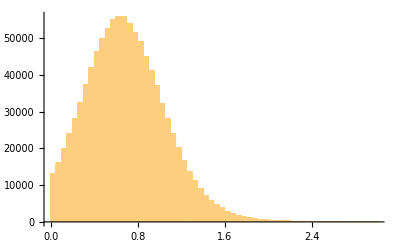

0.703164

0.388045

```mathematica
Histogram[concSb2O3D3,{0.0,3,0.05}]
Mean[concSb2O3D3]
StandardDeviation[concSb2O3D3]
```

```mathematica
list =HistogramList[concSb2O3D3,{0.0,100,0.05}];
threshold=1.4;  (* based on D3 *)
indexThreshold=Position[list[[1]],p_?(#==threshold&)][[1,1]]
volPercentNumerator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,indexThreshold,Length[list[[1]]]-1}];
volPercentDenominator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,1,Length[list[[1]]]-1}];
volPercentNumerator = Total[volPercentNumerator]
volPercentDenominator = Total[volPercentDenominator]
fractionSb2O3inlumps = 100*volPercentNumerator/volPercentDenominator
```

29

63208.1

703241.

8.98811

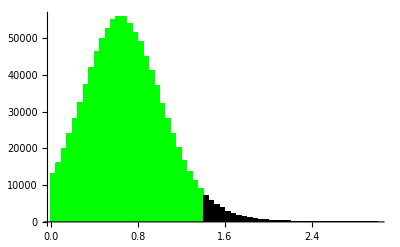

```mathematica
listBelowThreshold = Histogram[Select[concSb2O3D3,#<threshold &],{0,3,0.05},ChartStyle->Directive[Green,EdgeForm[]]];
listAboveThreshold = Histogram[Select[concSb2O3D3,#>=threshold &],{0,3,0.05},ChartStyle->Directive[Black,EdgeForm[]]];
gSb2O3D3=Show[{listBelowThreshold,listAboveThreshold}]
```

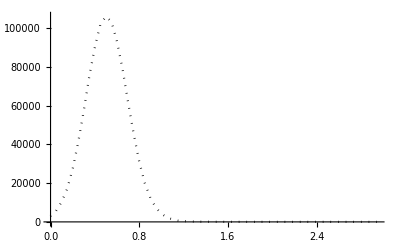
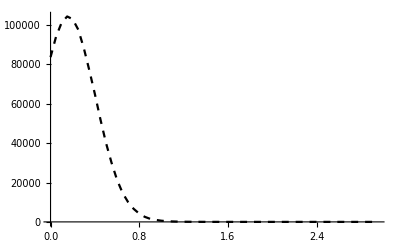
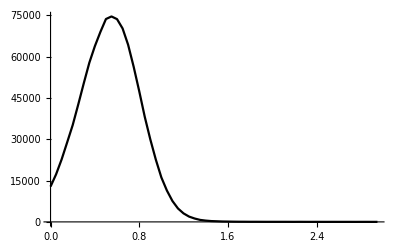

```mathematica
data =HistogramList[concSb2O3A1,{0,3,0.05}];
gSb2O3A1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dotted]];
data =HistogramList[concSb2O3C1,{0,3,0.05}];
gSb2O3C1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dashed]];
data =HistogramList[concSb2O3D1,{0,3,0.05}];
gSb2O3D1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black]];
{gSb2O3A1,gSb2O3C1,gSb2O3D1}
```

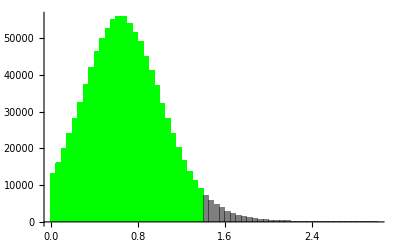

```mathematica
gHistD3=Histogram[{
Select[concSb2O3D3,#<threshold &],
Select[concSb2O3D3,#>=threshold &]},{0,3,0.05},
ChartStyle->{ Directive[Green,Opacity[1],EdgeForm[]],Directive[Black,EdgeForm[]]}]
```

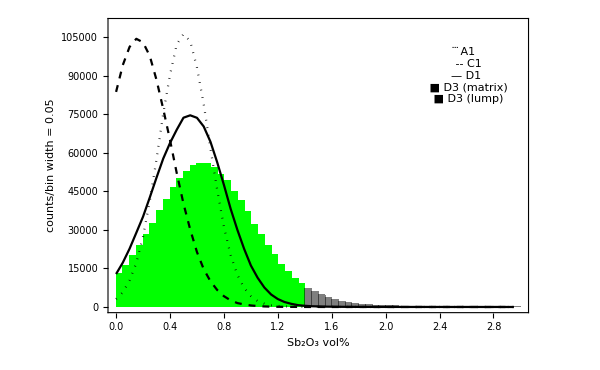

```mathematica
Show[{gHistD3,gSb2O3D1,gSb2O3A1,gSb2O3C1},PlotRange->{{0,3},{0,110000}},
Frame->True,FrameStyle->14,ImageSize->600,
FrameLabel->{{"counts/bin width = 0.05",""},{"Sb_2O_3 vol%",""}},
Epilog->Style[Text[Framed[" ⃛ A1\n -- C1\n— D1\n ■ D3 (matrix)\n ■ D3 (lump)"],{2.6,90000}],16,TextAlignment->Right]]
```

```mathematica
TableForm[
{{"A1", Mean[concSb2O3A1],StandardDeviation[concSb2O3A1],Max[concSb2O3A1]},
{"C1", Mean[concSb2O3C1],StandardDeviation[concSb2O3C1],Max[concSb2O3C1]},
{"D1", Mean[concSb2O3D1],StandardDeviation[concSb2O3D1],Max[concSb2O3D1]},
{"D3", Mean[concSb2O3D3],StandardDeviation[concSb2O3D3],Max[concSb2O3D3]}}, 
TableHeadings->{None,{"sample","average","standard deviation", "maximum"}}]

TableForm[
{{"D3", threshold,fractionSb2O3inlumps}}, 
TableHeadings->{None,{"sample","threshold","fraction in lumps"}}]
```

sample | average | standard deviation | maximum
A1 | 0.536193 | 0.193723 | 10.0555
C1 | 0.283623 | 0.18809 | 2.52449
D1 | 0.570951 | 0.271951 | 10.3326
D3 | 0.703164 | 0.388045 | 15.0781

sample | threshold | fraction in lumps
D3 | 1.4 | 8.98811